```mathematica
Manipulate[
Module[{x,y,h,δ,c0,δc,c1,c2,f,g,h1,h2,dA1,dA2,hA1,hA2,dB1,dB2,hB1,hB2,dC1,dC2,hC1,hC2},
x=1;y=0.4*x;h=0.65*y;δ=0.05;

c0={{0.25*x,y},{0.5*x,0.5*y},{0.75*x,y}};
δc={{δ,0},{0,δ},{-δ,0}};
c1=c0+δc;c2=c0-δc;

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[c[[1,1]],c[[-1,1]],0.01];
h1=Join[{c2[[1]]},g@c1];h2=Join[g@c2,{c1[[-1]]}];

(*dA1={#,Quiet@Interpolation[g[c1]][#]}&/@Range[c1[[1,1]],0.5*x,0.02];
dA2={#,Quiet@Interpolation[g[c2]][#]}&/@Range[c2[[1,1]],0.5*x,0.02];
hA1=Join[{dA2[[1]]},dA1];hA2=Join[dA2,{dA1[[-1]]}];

dB1={#,Quiet@Interpolation[g[c1]][#]}&/@Range[0.5*x,c1[[-1,1]],0.02];
dB2={#,Quiet@Interpolation[g[c2]][#]}&/@Range[0.5*x,c2[[-1,1]],0.02];
hB1=Join[{dB2[[1]]},dB1];hB2=Join[dB2,{dB1[[-1]]}];*)

dC1={#,Quiet@Interpolation[g[c1]][#]}&/@Range[(c1[[1,1]]+0.5*x)/2,(0.5*x+c1[[-1,1]])/2,0.02];
dC2={#,Quiet@Interpolation[g[c2]][#]}&/@Range[(c2[[1,1]]+0.5*x)/2,(0.5*x+c2[[-1,1]])/2,0.02];
hC1=Join[{dC2[[1]]},dC1];hC2=Join[dC2,{dC1[[-1]]}];

Graphics[{Thick,
BezierCurve@c1,BezierCurve@c2,
(*Blue,Line@dA1,Red,Line@dA2,
Green,Line@dB1,Black,Line@dB2,*)
(*FaceForm@Opacity[0.5,Gray],Polygon@Join[hA1,hA2]*)
(*Dashed,Green,Line@hB1,Orange,Line@hB2,*)
(*FaceForm@Yellow,Polygon@Join[hA1,hA2],FaceForm@Orange,Polygon@Join[hB1,hB2]*)
Blue,Line@dC1,Red,Line@dC2,Polygon@Join[hC1,hC2]
},ImageSize->500]
],
Control[{{q,0.2,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
(0.3+0.5)/2
```

```mathematica
Manipulate[
Module[{x,y,h,δ,V,L,vaporize,condense,head},
x=1;y=0.4*x;h=0.65*y;(*δ=0.25/5;*)δ=0.05;

V=Module[{c0,δc,c1,c2,f,g,h1,h2},
c0={{0,y/2},{0.42*x,y/2},{0.75*x,0.4*y},{0.75*x,0.75*y},{0.75*x,y}};
δc={{0,δ},{-δ,δ},{-δ,δ},{-δ,δ},{-δ,0}};
c1=c0+δc;c2=c0-δc;

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[0,c[[-1,1]],0.01];
h1=Join[{c2[[1]]},g@c1];h2=Join[g@c2,{c1[[-1]]}];

Graphics[{Green,Point@RandomPoint[Polygon@Join[h1,h2],Round[(1-q)*500]]}]];

L=Module[{c0,δc,c1,c2,f,g,h1,h2},
c0={{0,y/2},{0.25*x,y/2},{0.25*x,0}};
δc={{0,δ},{δ,δ},{δ,0}};
c1=c0+δc;c2=c0-δc;

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[0,c[[-1,1]],0.01];
h1=Join[{c2[[1]]},g@c1];h2=Join[g@c2,{c1[[-1]]}];

Graphics[{Blue,Point@RandomPoint[Polygon@Join[h1,h2],Round[q*500]]}]];

vaporize=Module[{c0,δc,c1,c2,f,g,h1,h2},
c0={{0.25*x,y},{0.5*x,0.5*y},{0.75*x,y}};
δc={{δ,0},{0,δ},{-δ,0}};
c1=c0+δc;c2=c0-δc;

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[c[[1,1]],c[[-1,1]],0.01];
h1=Join[{c2[[1]]},g@c1];h2=Join[g@c2,{c1[[-1]]}];

Graphics[{Thick,BezierCurve@c1,BezierCurve@c2,Polygon@Join[h1,h2](*Point@RandomPoint[Polygon@Join[h1,h2],250]*)}]
];

head[col_,i_]:=Graphics[{Thick,col,Line[{{0,0},{0.5,i*(√3)/2},{1,0}}]},ImageSize->{50,25},AspectRatio->Full];

Show[Graphics[{
EdgeForm@Thick,FaceForm@None,Rectangle[{0,0},{x,y}],
{Blue,
Point@RandomPoint[Polygon[{{0.25*x-δ,y+h},{0.25*x-δ,0},{0.25*x+δ,0},{0.25*x+δ,y+h}}],250],
Point@RandomPoint[Polygon[{{0.25*x-δ,0},{0.25*x-δ,-h},{0.25*x+δ,-h},{0.25*x+δ,0}}],100+Round[q*500]]},
{Green,
Point@RandomPoint[Polygon[{{0.75*x-δ,-h},{0.75*x-δ,y},{0.75*x+δ,y},{0.75*x+δ,-h}}],250],
Point@RandomPoint[Polygon[{{0.75*x-δ,y},{0.75*x-δ,y+h},{0.75*x+δ,y+h},{0.75*x+δ,y}}],100+Round[(1-q)*500]]},
Thick,
Blue,Line[{{0.25*x-1.5*δ,-h},{0.25*x,-h-0.2*h},{0.25*x+1.5*δ,-h}}],
Green,Line[{{0.75-1.5*δ,y+h},{0.75*x,y+1.2*h},{0.75*x+1.5*δ,y+h}}],
(*Inset[head[Blue,-1],{0.25*x,y},{0.5,-1}]*)
}],
L,V,PlotRange->All]
],
Control[{{q,0.2,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Quiet@Graphics[{
Directive[Blue,AbsolutePointSize[1]],Point[RandomPoint[ImplicitRegion[Between[y,{{Cos[x],Sin[x]},{Sin[x],Cos[x]}}],{{x,0,2 π},{y,-1,1}}],Round[q*10000]]]
},Frame->True],
Control[{{q,0.5},0.1,1,0.1}]
]
```

```mathematica
Manipulate[
Module[{c1,c2,f,g},
c1={{0,0},{2,0},{2,1}};
c2={{0,0.25},{1.75,0.25},{1.75,1}};

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:=Quiet@Interpolation[{#,f[c][#]}&/@Range[c[[1,1]],c[[-1,1]],0.01]];

Graphics[{Thick,
BezierCurve@c1,Red,BezierCurve@c2,
Point@RandomPoint[ImplicitRegion[Between[y,{g[c1][x],g[c2][x]}],{{x,0,2},{y,0,1}}],500]
(*Red,Dashed,Line@g[c1],Line@g[c2]*)
}]
],
Control[{{q,0.2,"feed quality"},0,1,0.1,Appearance->"Labeled"}]
]
```

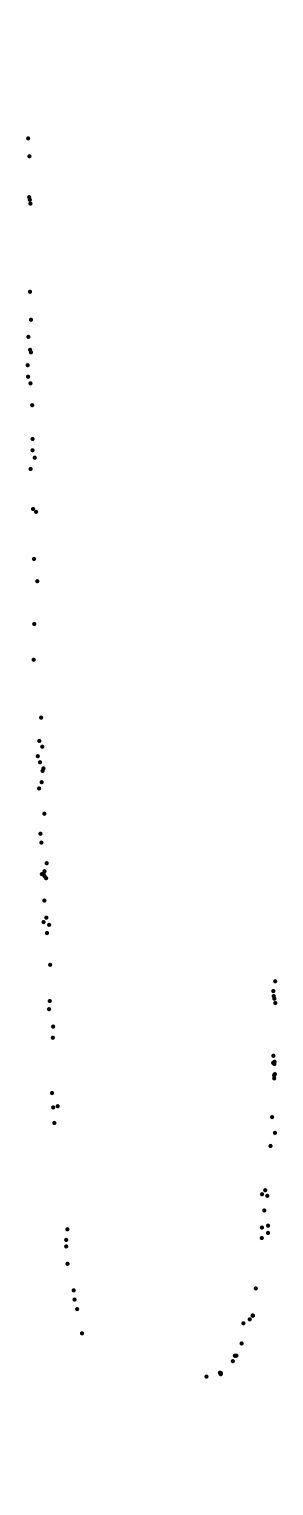

```mathematica
Module[{c1,c2,f,g,h1,h2},
c1={{0,0},{2,0},{2,1}};
c2={{0,0.25},{1.75,0.25},{1.75,1}};

f[c_]:=Quiet@Interpolation[BezierFunction[c][#]&/@Range[0,1,0.01]];
g[c_]:={#,f[c][#]}&/@Range[c[[1,1]],c[[-1,1]],0.01];

h1=Fit[g[c1],{1,x,x^2,x^3,x^4,x^5,x^6},x]/.x->z;
h2=Fit[g[c2],{1,x,x^2,x^3,x^4,x^5,x^6},x]/.x->z;

Show[
ListPlot[{g[c1],g[c2]},Joined->True,PlotStyle->{{Thick,Black},{Thick,Blue}}],
Plot[h1,{z,0,2},PlotStyle->{Thick,Dashed,Green},PlotRange->All],
Plot[h2,{z,0,1.75},PlotStyle->{Thick,Dashed,Red},PlotRange->All],
PlotRange->All];

Graphics[{Point@RandomPoint[ImplicitRegion[Between[y,{h1,h2}],{z,y}],100]}]
]
```